```mathematica
deck1 = Range[8,14];
deck = Table[deck1, {4}];
For[i=1,i<Length[deck]+1,i++, deck[[i]] = deck[[i]] + i*100   ];
deck= Sort[Join[deck[[1]], deck[[1]],deck[[2]],deck[[2]],deck[[3]],deck[[3]], deck[[4]], deck[[4]]]];   (*This is 2 set of decks ranging from 8 to A*)
hands = Subsets[deck, {5}];
```

```mathematica
(*three of a kind*)
Clear[threeKindQ];
threeKindQ[{___,x_,x_,x_,x_,___}]:=False; (* four of a kind *)
threeKindQ[{x_,x_,x_,y_,y_}/; x ≠ y] := False;
threeKindQ[{x_,x_,y_,y_,y_}/; x ≠ y] := False;
(*full hand*)
threeKindQ[{___,x_,x_,x_,___}]:=True; (* three of a kind *)
threeKindQ[{___}]:=False ; (* else *)
threeKindQs[h_] := threeKindQ[Sort[Mod[h,100]]]; 
(Count[hands, _? (threeKindQs)])/ Length[hands]
```

2240/22737

```mathematica
(*straight flush*)
Clear[straightFlush];
straightFlush[h_]:=h-h[[1]]=={0,1,2,3,4};
(*straightsFlush[h_] :=straightFlush[h]; *)
Count[hands, _? (straightFlush)] / Length[hands]
```

16/159159

```mathematica
(*straight*)
Clear[straight];
amountStraightFlush  = Count[hands, _? (straightFlush)];
straight[h_] :=  MatchQ[h-h[[1]],{0,1,2,3,4}];
straights[v_] := straight[Sort[Mod[v,100]]];
(Count[hands, _? (straights)]-amountStraightFlush)/ Length[hands]
```

1360/53053

```mathematica
(*flush*)
Clear[flush]
amountStFlu = Count[hands, _? (straightFlush)]
flush[h_] := Equal@@ Quotient[h,100];
countFlush = (Count[hands, _? (flush)]-amountStFlu)/ Length[hands]
```

384

953/477477

```mathematica
(*a pair*)
Clear[pairQ]
(*pairQ[{___,x_,x_,y_,y_,___}/;x≠y]:=False;*)
pairQ[{___,x_,x_,___,y_,y_,___}/;x≠y]:=False; (* two pairs *)
pairQ[{___,x_,x_,x_, ___}]:=False;(* three of a kind *)
(***function for flush***)
pairQ[{___,x_,x_,___}]:=True; (* a pair *)
pairQ[{___}]:=False ; (* else *)
pairQs[h_] := pairQ[Sort[Mod[h,100]]] &&(!flush[h]);
(Count[hands, _? (pairQs)])/ 
Length[hands]
```

35840/68211

```mathematica
Clear[nothing]
nothing[{___,x_,x_,___,y_,y_,___}/;x≠y]:=False;
nothing[{___,x_,x_,x_,x_,___}]:=False;
nothing[{___}]:=True ;(* else *)
nothings[h_] := nothing[Sort[h]]&&(!flush[h])&&(!straight[Sort[h]])
(Count[hands, _? (nothings)])/ 
Length[hands]
```

67732/68211

```mathematica
(*------------------------Part b------------------------*)

(*full house*)
fullHouse= Binomial[7,1]*Binomial[8,3]*Binomial[6,1]*Binomial[8,2]/Binomial[56,5]
```

392/22737

```mathematica
(*3 kind*)
threeKind = (Binomial[7,1]*Binomial[8,3]*Binomial[48,2]/Binomial[56,5]) - fullHouse
```

2240/22737

```mathematica
(*4 kind*)
fourKind = Binomial[7,1]*Binomial[8,4]*Binomial[48,1]/Binomial[56,5]
```

140/22737

```mathematica
(*5 kind*)
fiveKind = Binomial[7,1]*Binomial[8,5]/Binomial[56,5]
```

7/68211

```mathematica
(*one pair*)
onePair = Binomial[7,1]*Binomial[8,2]*Binomial[6,3]*Binomial[8,1]^3/Binomial[56,5]
```

35840/68211

```mathematica
(*straight flush*)
straightFlush = Binomial[3,1]*Binomial[8,1]*16/Binomial[56,5]
(*testa 6 över 1*)
```

16/159159

```mathematica
(*straight*)
straight = (Binomial[3,1]*Binomial[8,1]^5-Binomial[3,1]*Binomial[8,1]*16)/Binomial[56,5]
```

1360/53053

```mathematica
(*flush*)
(Binomial[14,5]*Binomial[4,1]-Binomial[3,1]*Binomial[8,1]*16)/Binomial[56,5]
```

953/477477

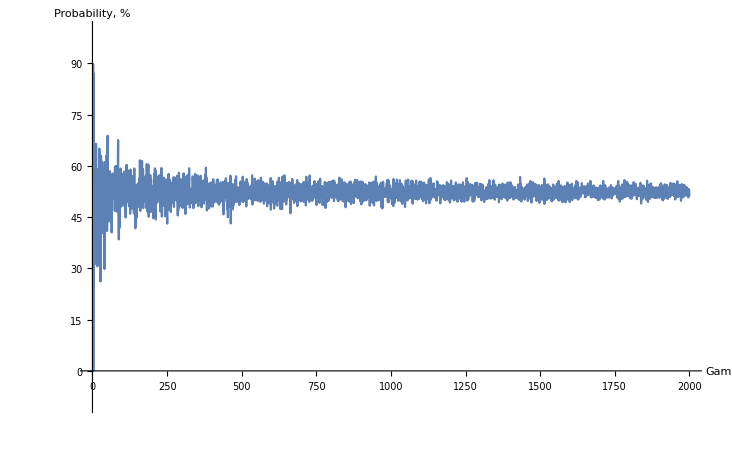

```mathematica
(*------------------------Part c------------------------*)
(*straight flush*)
Clear[straightFlush]
straightFlush[h_]:=h-h[[1]]=={0,1,2,3,4};
(*flush*)
Clear[flush]
flush[h_] := (!straightFlush[h]) &&Equal@@ Quotient[h,100];
(*a pair*)
Clear[pairQ]
(*pairQ[{___,x_,x_,y_,y_,___}/;x≠y]:=False;*)
pairQ[{___,x_,x_,___,y_,y_,___}/;x≠y]:=False; (* two pairs *)
pairQ[{___,x_,x_,x_, ___}]:=False;
(***function for flush***)
pairQ[{___,x_,x_,___}]:=True; (* a pair *)
pairQ[{___}]:=False ; (* else *)

pairQs[h_] := pairQ[Sort[Mod[h,100]]] &&(!flush[h]);

deck1 = Range[8,14];
deck = Table[deck1, {4}];
For[i=1,i<Length[deck]+1,i++, deck[[i]] = deck[[i]] + i*100   ];
deck= Sort[Join[deck[[1]], deck[[1]],deck[[2]],deck[[2]],deck[[3]],deck[[3]], deck[[4]], deck[[4]]]];

hand:=RandomSample[deck,5];
(*Clear[nf]*)
(*n= 2000;*)
(*
omega := Sort/@Table[hand,{n}];  (*1000 hands*)
nf= Count[omega, _?(pairQs)];
nf/n;
*)
(*-------------------------------------------------*)
Clear[play]
play := Sort/@Partition[RandomSample[deck, 5], 5] 
(*It's 4 hands times 5 cards*)
(*pairQ/@play*)
Clear[omega3]
omega3[n_] := Table[play, {n}];  (* n x play where play is four players with 5 cards each hand*)
Clear[pair3]
pair3[play_] := Or@@pairQs/@play
Clear[p3]
p3[n_] := (Count[omega3[n], _?(pair3)]*100)/(n);
Plot[p3[n],{n,1,2000}, AxesLabel->{"Game", "Probability, %"}, PlotRange->{-0.1*100,1*100}]
```